## Вариант 13

### Задание 1

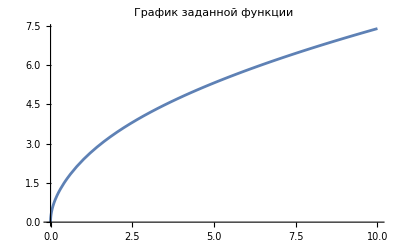

```mathematica
f[x_]:= √(5*x+Log[x^2+1]);
Subscript[x, 0]=2.47;
initialPlot=Plot[f[x],{x, 0,10},PlotLabel -> "График заданной функции"];
Show[initialPlot]
```

#### а) функция D системы Mathematica

```mathematica
Print["Производная 1-го порядка: ", d1=D[f[x],x]/.x->Subscript[x, 0]]
Print["Производная 2-го порядка: ", d2=D[f[x],{x,2}]/.x->Subscript[x, 0] ]
```

Производная 1-го порядка: 0.752823

Производная 2-го порядка: -0.17656

#### б) формулы численного дифференцирования

```mathematica
FiniteDifference1[y_,y1_]:=y1-y; 
FiniteDifference2[y_,y1_,y2_]:=y2-2y1+y;
FiniteDifference3[y_,y1_,y2_,y3_]:=y3-3y2+3y1-y;
```

```mathematica
h1=0.1;
```

```mathematica
y1=1/h1(FiniteDifference1[f[Subscript[x, 0]],f[Subscript[x, 0]+h1]]-1/2*FiniteDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h1],f[Subscript[x, 0]+2h1]]+1/3*FiniteDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h1],f[Subscript[x, 0]+2h1], f[Subscript[x, 0]+3h1]]);
```

```mathematica
y2=1/h1^2(FiniteDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h1],f[Subscript[x, 0]+2h1]]-FiniteDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h1],f[Subscript[x, 0]+2h1], f[Subscript[x, 0]+3h1]]);
```

```mathematica
Print["Производная 1-го порядка: ", y1]
Print["Производная 2-го порядка: ", y2]

Print["Разница между вычисленными значениями 1-й производной: ",Abs[d1-y1]]
Print["Разница между вычисленными значениями 2-й производной: ",Abs[d2-y2]]
```

Производная 1-го порядка: 0.752798

Производная 2-го порядка: -0.175613

Разница между вычисленными значениями 1-й производной: 0.0000254426

Разница между вычисленными значениями 2-й производной: 0.000946301

```mathematica
h2=0.01;
```

```mathematica
y1=1/h2(FiniteDifference1[f[Subscript[x, 0]],f[Subscript[x, 0]+h2]]-1/2*FiniteDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h2],f[Subscript[x, 0]+2h2]]+1/3*FiniteDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h2],f[Subscript[x, 0]+2h2], f[Subscript[x, 0]+3h2]]);
y2=1/h2^2(FiniteDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h2],f[Subscript[x, 0]+2h2]]-FiniteDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h2],f[Subscript[x, 0]+2h2], f[Subscript[x, 0]+3h2]]);
```

```mathematica
Print["Производная 1-го порядка: ", y1]
Print["Производная 2-го порядка: ", y2]

Print["Разница между вычисленными значениями 1-й производной: ",Abs[d1-y1]]
Print["Разница между вычисленными значениями 2-й производной: ",Abs[d2-y2]]
```

Производная 1-го порядка: 0.752823

Производная 2-го порядка: -0.176549

Разница между вычисленными значениями 1-й производной: 2.9197×10^-8

Разница между вычисленными значениями 2-й производной: 0.0000107209

Следовательно, уменьшение шага позволяет получить более точные результаты

### Задание 2

#### а)

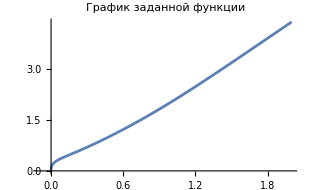

```mathematica
f[x_]:=((12 x^3+x)^(1/3))/(√(1+(x^3+2)^-1))
Plot[f[x], {x,-0.1,2},PlotLabel -> "График заданной функции"]
```

Так как изначальная функция определена не на всем множестве R, расчёты дают комплексные значения, которые невозможно будет сравнить.
Функция заменена на следующую для устранения разрывов и обеспечения области определения R :

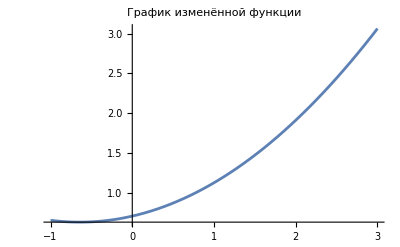

```mathematica
f[x_]:=1/(√2)+x/(3 √2)+(7 x^2)/(27 √2)
Plot[f[x], {x,-1,3},PlotLabel -> "График изменённой функции"]
```

```mathematica
a=-1;
b=3;
h=0.2;
data=Table[{x,(f[x+h]-f[x-h])/(2h)},{x,a,b,h}];
TableForm[data,TableHeadings->{None,{"x_i","y'_i"}}]
```

x_i | y'_i
-1. | -0.130946
-0.8 | -0.0576161
-0.6 | 0.0157135
-0.4 | 0.0890431
-0.2 | 0.162373
0. | 0.235702
0.2 | 0.309032
0.4 | 0.382361
0.6 | 0.455691
0.8 | 0.529021
1. | 0.60235
1.2 | 0.67568
1.4 | 0.749009
1.6 | 0.822339
1.8 | 0.895669
2. | 0.968998
2.2 | 1.04233
2.4 | 1.11566
2.6 | 1.18899
2.8 | 1.26232
3. | 1.33565

#### б)

```mathematica
Derivate=D[f[x],x]
```

1/(3 √2)+(7 √2 x)/27

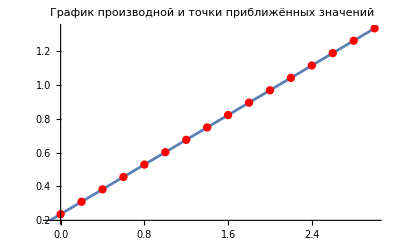

```mathematica
graph=Plot[Derivate,{x,-0.1,3}];
points=ListPlot[data,PlotStyle->{PointSize[0.015],Red}];
Show[graph,points, PlotLabel-> "График производной и точки приближённых значений"]
```

### Задание 3

#### а) Метод средних прямоугольников

```mathematica
f[x_]:=(x+√(1.4x+3.1))/(3+√(x^2+2.7))
a=0.8;
b=1.6;
Subscript[x, 0]=a;
```

```mathematica
n1=8;
step=(b-a)/n1;
For[i=1,i<=n1,i++, Subscript[x, i]=step+Subscript[x, i-1];]
AverageRectangle1=(b-a)/n1*∑_(i=1)^n1 f[Subscript[x, i-1]+(b-a)/(2*n1)]
```

0.536085

```mathematica
n2=10;
step=(b-a)/n2;
For[i=1,i<=n2,i++, Subscript[x, i]=step+Subscript[x, i-1];]
AverageRectangle2=(b-a)/n2*∑_(i=1)^n2 f[Subscript[x, i-1]+(b-a)/(2*n2)]
```

0.536074

Уточнение по Ричардсону

```mathematica
k=2;
Richardson=AverageRectangle2+n1^k/(n2^k-n1^k)(AverageRectangle2-AverageRectangle1)
```

0.536054

#### б) Метод трапеций

```mathematica
n1=8;
Subscript[x, 0]=a;
step=(b-a)/n1;
For[i=1,i<=n1,i++, Subscript[x, i]=step+Subscript[x, i-1];]
Trapezoidal1=(b-a)/n1*(∑_(i=1)^(n1-1) f[Subscript[x, i]]+f[Subscript[x, 0]]/2+f[Subscript[x, n1]]/2)
```

0.535991

```mathematica
n2=10;
Subscript[x, 0]=a;
step=(b-a)/n2;
For[i=1,i<=n2,i++,
Subscript[x, i]=step+Subscript[x, i-1];]
Trapezoidal2=(b-a)/n2*(∑_(i=1)^(n2-1) f[Subscript[x, i]]+f[Subscript[x, 0]]/2+f[Subscript[x, n2]]/2)
```

0.536014

Уточнение по Ричардсону

```mathematica
Richardson=Trapezoidal2+n1^k/(n2^k-n1^k)(Trapezoidal2-Trapezoidal1)
```

0.536054

### Задание 4

#### Разбиение отрезка интегрирования на 8 частей

```mathematica
data=({{-0.5, 0.5359}, {-0.34, 0.4371}, {-0.18, 0.3017}, {-0.02, 0.0735}, {0.14, 0.2839}, {0.3, 0.4977}, {0.46, 0.6981}, {0.62, 0.8984}, {0.78, 1.1044}});
```

```mathematica
a=-0.5;
b=0.78;
n=4;
h=(b-a)/(2n)
```

0.16

```mathematica
For[i=0,i<=2*n,i++, Subscript[y, i]=data[[i+1,2]];]
```

```mathematica
Simpsons=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

0.631173

#### Разбиение отрезка интегрирования на 16 частей

```mathematica
data=({{-0.5, 0.5359}, {-0.42, 0.4851}, {-0.34, 0.4371}, {-0.26, 0.3716}, {-0.18, 0.3017}, {-0.1, 0.2073}, {-0.02, 0.0735}, {0.06, 0.1555}, {0.14, 0.2839}, {0.22, 0.3901}, {0.3, 0.4977}, {0.38, 0.5925}, {0.46, 0.6981}, {0.54, 0.7899}, {0.62, 0.8984}, {0.7, 0.9905}, {0.78, 1.1044}});
```

```mathematica
n=8;
h=(b-a)/(2n)
For[i=0,i<=2*n,i++, Subscript[y, i]=data[[i+1,2]];]
```

0.08

```mathematica
Simpsons=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

0.638696

### Задание 5

#### Формула Гаусса (4 узла)

```mathematica
f[x_]=(x+1)Cos[x^2+2];
a=0.6;
b=2.5;
n=4;
polynomial = LegendreP[n,x]
```

1/8 (3-30 x^2+35 x^4)

```mathematica
soluton=NSolve[polynomial==0,x];
xx=x/.soluton
```

{-0.861136,-0.339981,0.339981,0.861136}

```mathematica
T=Table[If[i==1,1,(xx[[j]])^(i-1)],{i,n},{j,n}];MatrixForm[T]
```

(1 | 1 | 1 | 1
-0.861136 | -0.339981 | 0.339981 | 0.861136
0.741556 | 0.115587 | 0.115587 | 0.741556
-0.638581 | -0.0392974 | 0.0392974 | 0.638581)

```mathematica
B=Table[If[EvenQ[i]==True,0,2/i],{i,n}]//N
```

{2.,0.,0.666667,0.}

```mathematica
A=LinearSolve[T,B]
```

{0.347855,0.652145,0.652145,0.347855}

```mathematica
Integral=(b-a)/2*∑_(i=1)^n A[[i]]*f[(b+a)/2+(b-a)/2*xx[[i]]]
```

-0.217085